```mathematica
alphabet={a,b,c,d,e,f,g,h,i,j,k,k,m,n,o,p,q,r,s,t,u,v,w,x,y,z}
```

{a,b,c,d,e,f,ExpressionGraph[ConstantArray[x,#1],VertexLabels→None,GraphLayout→RadialEmbedding,EdgeShapeFunction→Line]&,h,i,j,k,k,m,n,o,p,q,r,s,t,u,v,w,{1,2,3,4},{2,3,4},z}

```mathematica
alphabet={a,b,c,d}
```

{a,b,c,d}

```mathematica
Fold
```

Fold

```mathematica
Fold[List,x,{a,b,c,d}]
```

{{{{{1,2,3,4},a},b},c},d}

```mathematica
alphabet={a,b,c,d}
perms=Permutations@alphabet
```

{a,b,c,d}

{{a,b,c,d},{a,b,d,c},{a,c,b,d},{a,c,d,b},{a,d,b,c},{a,d,c,b},{b,a,c,d},{b,a,d,c},{b,c,a,d},{b,c,d,a},{b,d,a,c},{b,d,c,a},{c,a,b,d},{c,a,d,b},{c,b,a,d},{c,b,d,a},{c,d,a,b},{c,d,b,a},{d,a,b,c},{d,a,c,b},{d,b,a,c},{d,b,c,a},{d,c,a,b},{d,c,b,a}}

```mathematica
6!
```

720

```mathematica
TreePlot[Fold[List,x,{a,b,c,d}],1]
```

TreePlot::graph: A graph object is expected at position 1 in TreePlot[{{{{{1,2,3,4},a},b},c},d},1].

TreePlot[{{{{{1,2,3,4},a},b},c},d},1]

{a,b,c}

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a}}

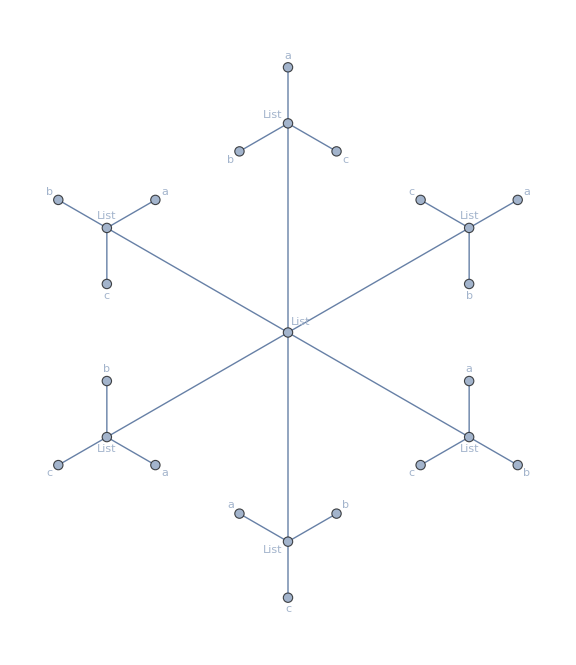

```mathematica
alphabet={a,b,c}
perms=Permutations@alphabet
theGraph=ExpressionGraph[perms,GraphLayout->"BalloonEmbedding",VertexLabels->Automatic]
```

```mathematica
EdgeCount[theGraph]
```

24

-Graphics-

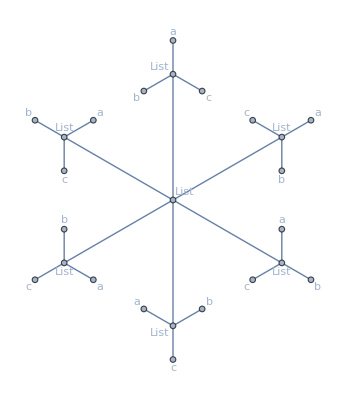
TreeGraph[-Graphics-,VertexLabels→Automatic]

```mathematica
TreeGraph[theGraph,VertexLabels->Automatic]
```

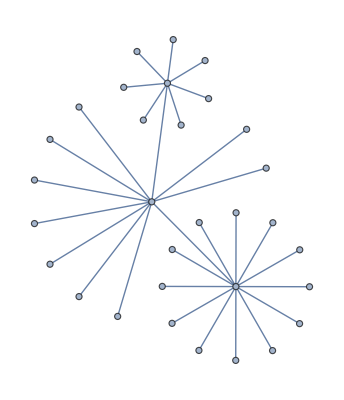

```mathematica
Graph[Table[Floor[j/12]<->j,{j,1,30}],GraphLayout->"BalloonEmbedding"]
```

```mathematica
alphabet={a,b,c}
perms=Permutations@alphabet
theGraph=ExpressionGraph[perms,GraphLayout->"BalloonEmbedding",VertexLabels->Automatic]
```

{a,b,c}

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a}}

-Graphics-

```mathematica
3
ClearAll[g]
g=GraphComputation`ExpressionGraph[ConstantArray[x,#],VertexLabels->None]&;
```

3

```mathematica
g=ExpressionGraph[ConstantArray[x,#],VertexLabels->None,]&;
```

```mathematica
g[Range[2,4]]
```

ExpressionGraph::intnm: Non-negative machine-sized integer expected at position 2 in ExpressionGraph[{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}},VertexLabels→None,Null].

ExpressionGraph[{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}},{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}},VertexLabels→None,Null]

```mathematica
SetProperty[g[{3,2,3,1,2,1,4}],{GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"}]
```

ExpressionGraph::intnm: Non-negative machine-sized integer expected at position 2 in ….

SetProperty::pvobj: … is not an object with properties.

SetProperty[ExpressionGraph[{{{{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}}},{{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}}}},{{{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}}},{{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}}}},{{{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}}},{{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}},{{{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}},{{{1,2,3,4},{1,2,3,4},{1,2,3,4},{1,2,3,4}}}}}}}},VertexLabels→None,Null],{GraphLayout→RadialEmbedding,EdgeShapeFunction→Line}]

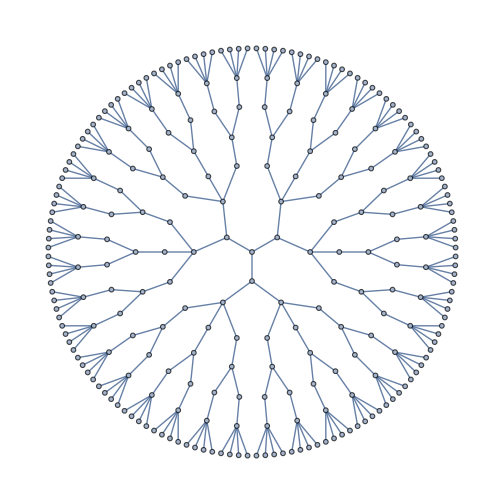
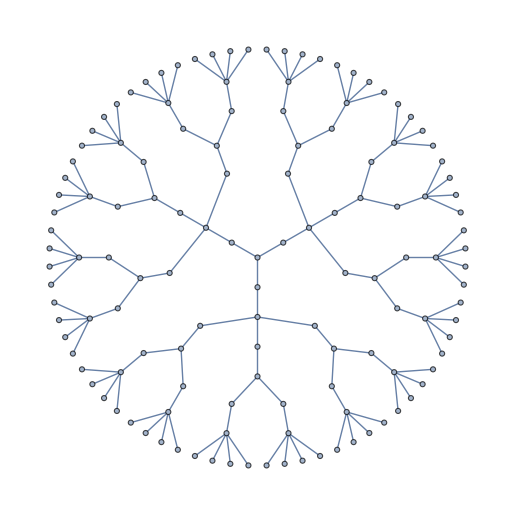

-Graphics- -Graphics-

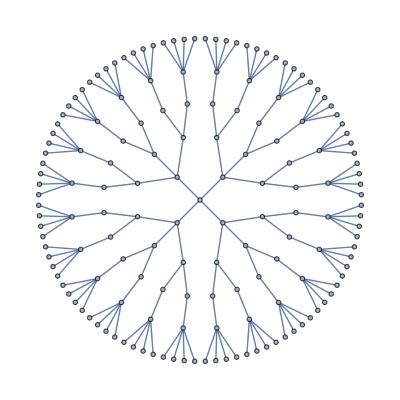

ConstantArray[x,#1]&

{{{{{1,2,3,4}},{{1,2,3,4}}},{{{1,2,3,4}},{{1,2,3,4}}},{{{1,2,3,4}},{{1,2,3,4}}}},{{{{1,2,3,4}},{{1,2,3,4}}},{{{1,2,3,4}},{{1,2,3,4}}},{{{1,2,3,4}},{{1,2,3,4}}}},{{{{1,2,3,4}},{{1,2,3,4}}},{{{1,2,3,4}},{{1,2,3,4}}},{{{1,2,3,4}},{{1,2,3,4}}}},{{{{1,2,3,4}},{{1,2,3,4}}},{{{1,2,3,4}},{{1,2,3,4}}},{{{1,2,3,4}},{{1,2,3,4}}}}}

{{2,1},{2,1},{2,1}}

```mathematica
g=ExpressionGraph[ConstantArray[x,#],VertexLabels->None,GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"]&;
g[{4,3,2,1}]
gsub=ConstantArray[x,#]&
gsub[{4,3,2,1}]
ConstantArray[{2,1},3]
```

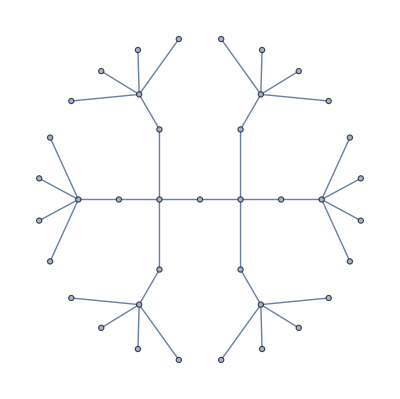

-Graphics-

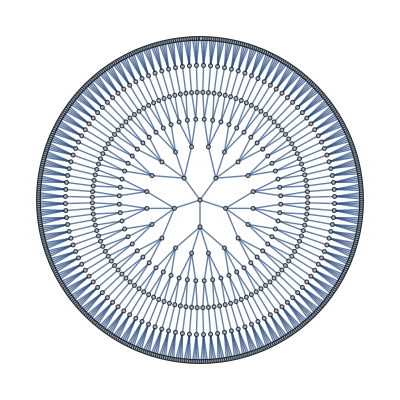

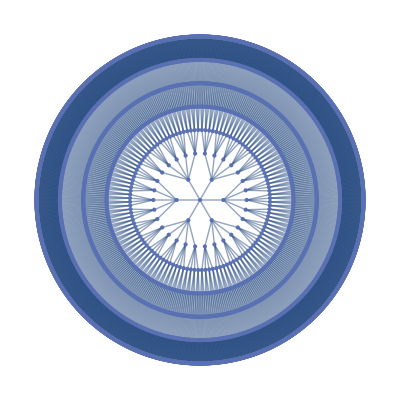

```mathematica
SetProperty[g[{2,3,1}],{GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"}]

SetProperty[g[{4,3,2,1}],{GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"}]

SetProperty[g[{5,4,3,2,1}],{GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"}]

SetProperty[g[{6,5,4,3,2,1}],{GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"}]
SetProperty[g[{8,7,5,4,3,2,1}],{GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"}]
```

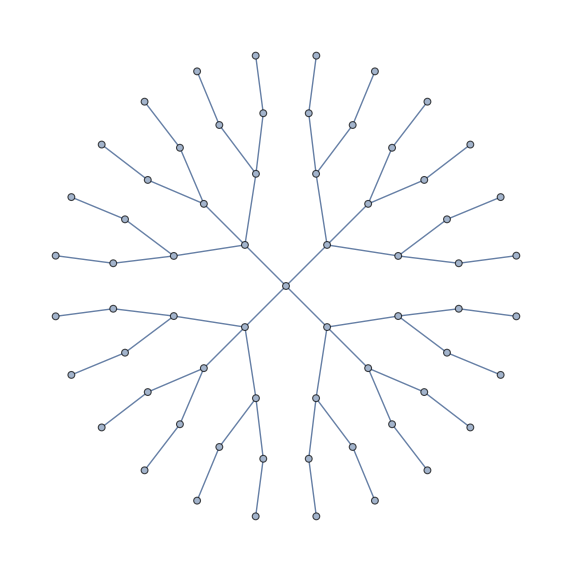
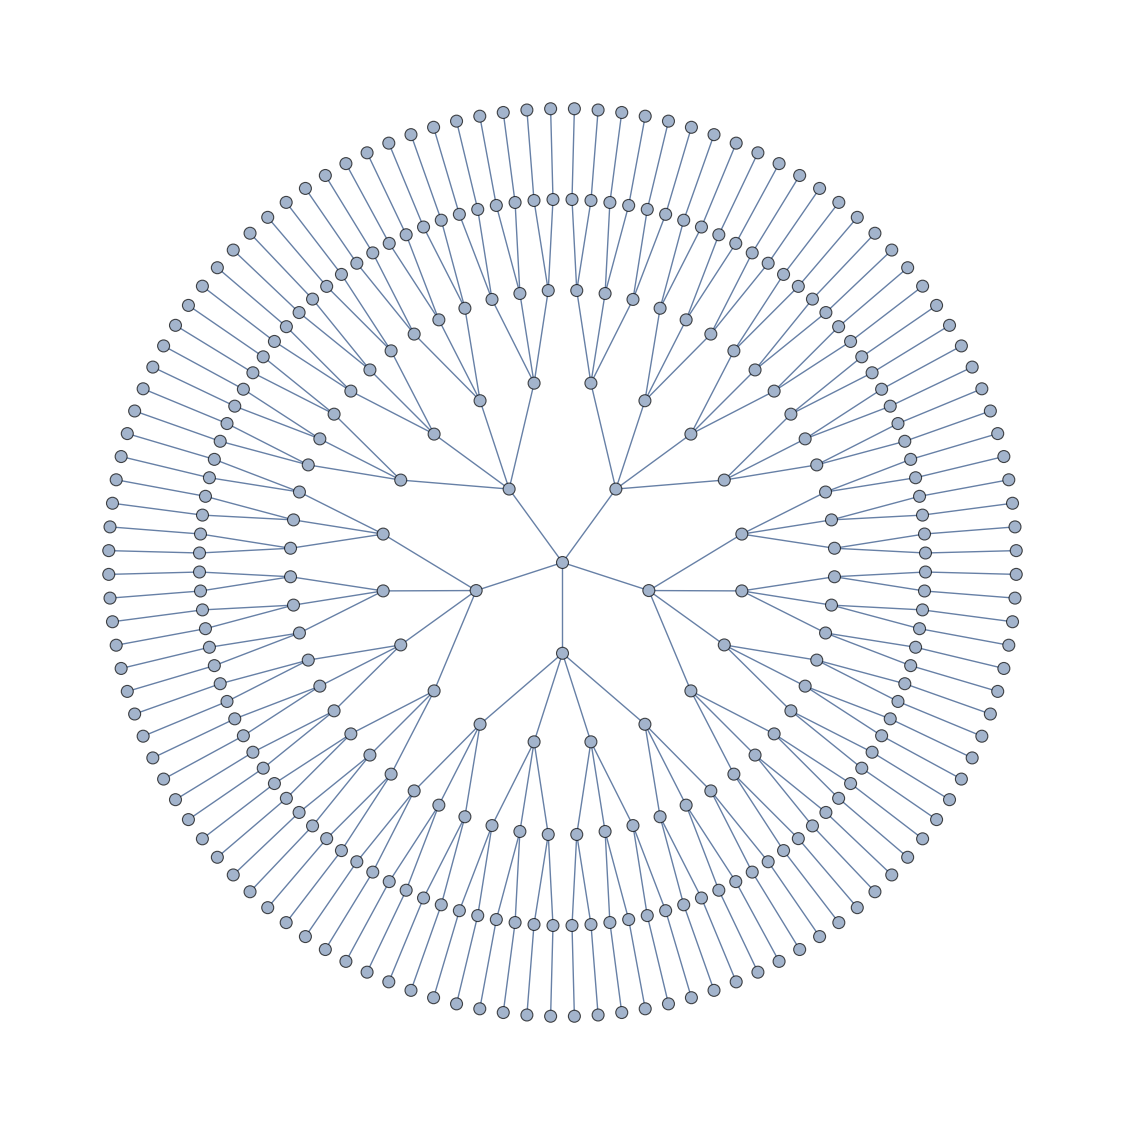

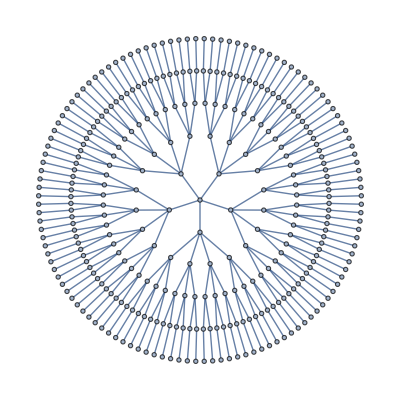

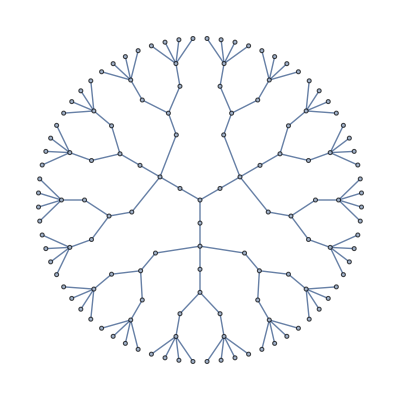

```mathematica
SetProperty[g[{3,1,3,1,2,1,4}],{GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"}]
```

```mathematica
Factorial[5]
```

120

```mathematica
f[][6]
```

EdgeList::graph: A graph object is expected at position 1 in ….

Graph[EdgeList[UndirectedEdge[{{{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}}},{{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}}}}]],GraphLayout→{BalloonEmbedding},ImageSize→Large]

```mathematica
f[][6,GraphLayout->{"RadialEmbedding"}]
```

EdgeList::graph: A graph object is expected at position 1 in ….

Graph[EdgeList[UndirectedEdge[{{{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}}},{{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}}}}]],GraphLayout→{RadialEmbedding},GraphLayout→{BalloonEmbedding},ImageSize→Large]

```mathematica
g1=f[Graph3D][6]
```

EdgeList::graph: A graph object is expected at position 1 in ….

Graph3D[EdgeList[UndirectedEdge[{{{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}}},{{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}},{{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}},{{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x},{x,x,x,x,x,x}}}}}]],GraphLayout→{BalloonEmbedding},ImageSize→Large]

```mathematica
g=ExpressionGraph[ConstantArray[x,#],VertexLabels->None,GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"]&;
g[{4,3,2,1}]
gsub=ConstantArray[x,#]&
gsub[{4,3,2,1}]
ConstantArray[{2,1},3]
f[##]&[x,y,z]
SetProperty[g[{5,4,3,2,1}],{GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"}]
```

f[x,y,z]

f[x]

ExpressionGraph[ConstantArray[x,#1]]&

ConstantArray[x,#1]&

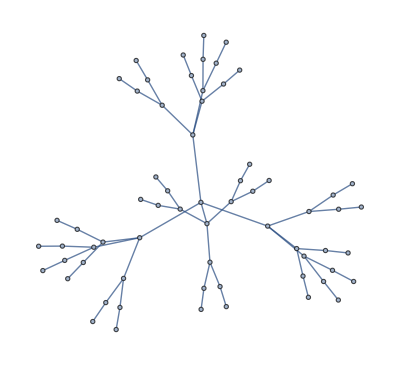

{{{{x},{x}},{{x},{x}},{{x},{x}}},{{{x},{x}},{{x},{x}},{{x},{x}}},{{{x},{x}},{{x},{x}},{{x},{x}}},{{{x},{x}},{{x},{x}},{{x},{x}}}}

```mathematica
f[#]&[x,y,z]
gsub=ExpressionGraph[ConstantArray[x,#]]&
gsub2=ConstantArray[x,#]&
gsub[{4,3,2,1}]
gsub2[{4,3,2,1}]
```

```mathematica
r
```

```mathematica
Module
```

```mathematica
gcd[list]:=
Module[{m=m0,n=n0},
While[n≠0,{m,n}={n,Mod[m,n]}];
m
]
```

```mathematica
Mod
```

```mathematica
Module[
{x=Table[i,{i,1,4}]},
While[ 
Length[x ]>0,
{x = Delete[x,1],
Print[x]}
];x
]
```

{2,3,4}

{3,4}

{4}

{}

{}

```mathematica
x={1,2,3,4}
y=  Delete[x,1]
```

{1,2,3,4}

{2,3,4}

{3,5,1,2,4,5,1,1,1,4,2,4,2,3,4,3,4,1,3,5,2,3,2,2,1,5,1,5,2,4,4,1,2,3,4,2,1,3,5,3,5,5,3,3,3,5,4,3,4,4,1,2,3,1,2,3,4,2,2,5,4,4,2,2,3,1,1,3,1,4,4,5,1,3,2,1,3,5,4,3,1,5,5,3,3,3,2,1,2,1,1,5,4,2,4,3,4,5,1,2,1,3,1,1,5,4,1,3,2,3,4,4,3,4,5,2,1,2,5,4,3,3,2,5,2,3,3,2,3,1,5,5,3,5,4,3,1,5,3,3,4,2,1,5,3,2,4,2,1,2,5,2,2,5,1,4,3,3,5,2,2,3,5,5,2,1,1,3,3,3,2,5,4,1,2,1,3,5,1,5,4,1,5,4,4,1,1,2,3,4,4,2,4,2,1,4,4,2,4,5,1,1,3,4,2,1,5,2,5,4,2,5,4,4,1,3,3,2,1,1,3,5,5,2,5,5,3,4,4,5,1,2,2,5,3,3,2,1,1,2,3,2,4,2,4,4,5,4,5,2,3,4,4,2,3,3,3,4,2,1,4,2,2,5,2,2,5,3,2,3,1,5,4,1,5,5,5,1,4,3,1,2,3,4,2,1,1,5,4,4,1,1,3,1,5,2,3,1,1,3,5,4,4,3,1,3,1,5,4,4,2,5,2,2,2,5,5,5,3,3,2,1,5,5,4,2,5,2,4,5,1,3,4,5,3,4,2,4,2,2,1,2,4,2,5,4,1,1,4,4,1,2,1,3,1,4,3,4,2,5,4,2,3,2,5,4,5,1,4,2,5,3,4,4,5,2,1,5,1,3,3,3,1,1,2,5,1,3,4,4,5,1,1,2,5,2,5,2,2,2,2,2,5,2,3,4,4,5,5,2,2,5,2,1,4,3,4,3,5,2,1,3,5,1,1,4,5,5,3,2,2,5,1,3,5,3,1,4,2,5,1,3,4,1,2,5,2,1,3,1,3,4,4,4,3,5,2,3,2,4,3,4,1,3,3,5,1,5,4,1,5,2,1,3,2,3,1,1,2,5,3,4,5,1,3,1,3,1,3,2,3,2,1,1,3,3,2,5,1,1,5,3,2,3,2,3,1,3,4,1,4,2,2,4,2,5,4,1,1,2,4,5,5,2,4,3,4,2,5,3,4,1,2,2,3,1,3,4,4,3,4,4,3,2,5,3,1,1,5,5,5,3,5,5,1,1,2,4,3,2,5,4,4,3,5,2,2,4,3,3,2,1,3,3,3,2,4,4,5,1,1,2,5,4,2,1,2,2,2,5,2,3,4,5,2,3,3,5,5,4,4,2,2,2,5,4,1,2,5,4,1,5,1,5,1,5,1,4,4,2,2,3,3,4,3,5,3,5,4,3,2,5,5,5,4,3,2,1,3,4,1,1,1,1,5,4,1,1,2,3,4,2,4,2,5,2,4,4,3,4,4,3,1,2,2,5,1,1,3,2,2,1,3,3,5,4,2,1,1,2,4,3,2,4,5,3,1,2,3,1,3,2,4,4,1,3,5,5,2,3,2,1,1,2,4,2,3,4,5,3,5,2,1,2,3,1,1,5,1,2,5,1,2,1,5,5,1,2,4,4,5,4,5,1,2,5,5,1,5,1,3,3,2,3,4,1,3,3,2,1,1,2,2,2,2,3,4,1,3,2,4,4,2,4,1,1,3,3,3,3,1,3,4,4,1,3,4,2,1,2,4,4,4,2,2,4,4,3,1,2,3,5,4,5,4,3,3,3,2,3,4,1,3,3,4,2,5,4,5,5,4,5,2,2,4,4,2,2,2,4,1,2,2,3,2,3,5,5,4,1,4,5,2,3,4,2,5,4,1,1,5,1,2,2,3,1,5,4,1,4,3,4,1,1,2,3,3,4,1,1,1,3,5,2,2,2,4,3,2,5,2,3,4,2,4,5,2,2,5,3,4,2,4,2,5,1,2,2,1,2,5,4,2,2,1,3,5,4,4,4,4,5,2,4,5,5,4,4,5,5,3,1,5,4,5,3,5,4,2,5,2,3,5,1,1,1,5,4,1,5,5,3,3,5,5,2,1,3,2,3,1,2,1,1,1,3,3,4,4,1,3,5,5,2,1,4,3,2,3,4,2,5,5,3,1,2,4,3,1,3,2,2,3,2,1,2,3,1,5,5,5,4,2,1,1,1,2,3,1,2,4,2,4,2,4,2,1,3,3,4}

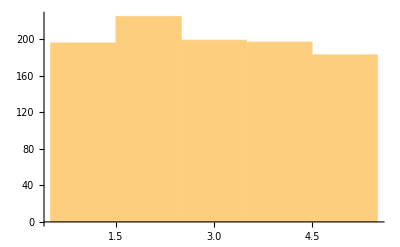

```mathematica
(*Check Randomness of Random Choice

*)
fiveRandomChecker=Table[RandomChoice@{5,4,3,2,1},{i,1,1000}]
Histogram@fiveRandomChecker
```

```mathematica
Module[
{x=Table[i,{i,1,5}],
y={}
},
While[ 
Length[x ]>0,
{x = Delete[x,1],
Print[x]}
];x
]
```

{2,3,4,5}

{3,4,5}

{4,5}

{5}

{}

{}

```mathematica
1
```

```mathematica
g=ExpressionGraph[ConstantArray[x,#],VertexLabels->None,GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"]&;

SetProperty[g[{4,3,2,1}],{GraphLayout->"RadialEmbedding",EdgeShapeFunction->"Line"}]
list={};
Recurse[source_,current_]:=
Module[
{
sourceAlpha=source,
currentAlpha=current,
currentBeta =Null
},
While[  
Length[sourceAlpha ]>0,
{
currentBeta=First[sourceAlpha],
AppendTo[currentAlpha,currentBeta],
sourceAlpha = DeleteCases[sourceAlpha,Alternatives@@currentBeta],
(*Print[sourceAlpha],*)
Recurse[sourceAlpha,currentAlpha]
}

];
AppendTo[list,currentAlpha]

]
```

-Graphics-

```mathematica
4!
```

24

```mathematica
Differen
```

```mathematica
DeleteCases[{5,4,3,2,1},Alternatives@@4]
```

{5,3,2,1}

```mathematica
list={};
Recurse[{5,4,3,2,1},{}]
```

{{1,3,2,4,5},{1,3,2,4,5},{1,3,2,4,5},{1,3,2,4,5},{1,3,2,4,5},{1,3,2,4,5},{1,3,2,4,5},{1,3,2,4,5},{1,3,4,5,2},{1,3,4,5,2},{1,3,4,5,2},{1,3,4,5,2},{1,3,4,5,2},{1,3,4,5,2},{1,3,4,5,2},{1,3,4,5,2},{1,4,3,2,5},{1,4,3,2,5},{1,4,3,2,5},{1,4,3,2,5},{1,4,3,2,5},{1,4,3,2,5},{1,4,3,2,5},{1,4,3,2,5},{1,4,5,3,2},{1,4,5,3,2},{1,4,5,3,2},{1,4,5,3,2},{1,4,5,3,2},{1,4,5,3,2},{1,4,5,3,2},{1,4,5,3,2}}

```mathematica
list={};
Recurse[{5,4,3,2,1},{}];
list
```

{{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2,1}}

```mathematica
foo={a,3}
First@foo
foo
```

{a,3}

a

{a,3}

```mathematica
Recurse[source_,current_]:=
Module[
{
sourceAlpha=source,
currentAlpha=current,
currentBeta =Null
},
While[  
Length[sourceAlpha ]>1,
{
currentBeta=RandomChoice[sourceAlpha],
AppendTo[currentAlpha,currentBeta],
(*Print[sourceAlpha],*)
Recurse[ Drop[sourceAlpha,Position[sourceAlpha,currentBeta][[1,1]]],currentAlpha]
}

];
AppendTo[list,currentAlpha]

]
```

```mathematica
list={};
Recurse[{5,4,3,2,1},{}];
list
```

{{}}

```mathematica
test={5,4,3,2,1}

Drop[test,Position[{5,4,3,2,1},4][[1,1]]]
```

```mathematica
{5,4,3,2,1}
Position[{5,4,3,2,1},4][[1,1]]
```

{5,4,3,2,1}

2

```mathematica
Position[{5,4,3,2,1},4][[1,1]]
```

2

```mathematica
Extract[{5,4,3,2,1},{{2}},{{2}}]
```

{{{2}}[4]}

```mathematica
Recurse[source_,current_]:=
Module[
{
sourceAlpha=source,
currentAlpha=current,
currentBeta =Null,
sentinel=Null
},
For[
i=0,
i<Length[sourceAlpha]+1, 
i++,
Drop[sourceAlpha,Position[sourceAlpha,currentBeta][[1,1]]]
]
]
```

```mathematica
(*Implement function to remove element from list, and return the list*)
```

```mathematica
listRemove[list_,index_]:=
Module[
{
returnedList={},
lengthOfList=Length[list],
nope={}
},
For[
i=1,
i<lengthOfList+1,
i++,
Print[returnedList];
If [
i!=index,
AppendTo[returnedList,list[[i]]]

]

];
returnedList
]
```

```mathematica
test= listRemove[{1,2,3,4,5},4]
```

{}

{1}

{1,2}

{1,2,3}

{1,2,3}

{1,2,3,5}

```mathematica
list ={};
Recurse[source_,current_]:=
Module[
{
indexCounter={},
sourceAlpha=source,
currentAlpha=current,
currentBeta =Null,
sentinel=Null
},
{
For[
i=1,
i<Length[sourceAlpha]+1, 
i++,
{
AppendTo[currentAlpha,source[[i]]];
Recurse[listRemove[source,i],currentAlpha]
}
];
AppendTo[list,currentAlpha]
}
]
```

```mathematica
(*use list return instead of Drop*)
```

```mathematica
list={};
Recurse[{5,4,3,2,1},{}];
list
```

{}

{}

{4}

{4,3}

{4,3,2}

{}

{}

{3}

{3,2}

{}

{}

{2}

{}

{}

{}

{{5,4,3,2,1},{5,4,3,2,1},{5,4,3,2},{5,4,3},{5,4},{5}}